## Resistor Calc

-Graphics-

```mathematica
Vref=1.23;
R10=47000;
R11=22000;
R9=330;
RpMax=5000;
RpMin=100;
```

```mathematica
(1.23(47000+1/(1/22000+1/5600)))/(1/(1/220000+1/5600))
```

11.5914

```mathematica
DpotR[input_]:=input 5600/128+110//N
```

```mathematica
Vout[input_]:=(Vref(R10+1/(1/R10+1/(R9+DpotR[input]))))/(1/(1/R11+1/(R9+DpotR[input])));
```

```mathematica
Vout[19]
```

49.3695

## Resistor Correction For Front Light

```mathematica
Vref=1.23;
R10=180000;
R11= 10000;
R9=5600;
RpMax=5000;
RpMin=100;
```

```mathematica
(1.23(47000+1/(1/22000+1/5600)))/(1/(1/220000+1/5600))
```

11.5914

```mathematica
DpotR[input_]:=input 5600/128+110//N
```

```mathematica
Vout[input_]:=(Vref(R10+1/(1/R10+1/(R9+DpotR[input]))))/(1/(1/R11+1/(R9+DpotR[input])));
```

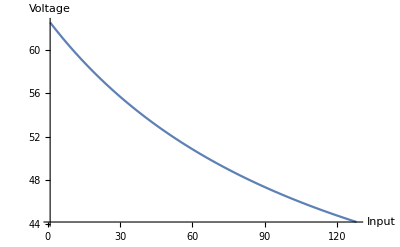

```mathematica
Plot[Vout[input],{input,1,128},AxesLabel->{"Input", "Voltage"}]
```

```mathematica
For[i=0,i<128,i++,Print[{i,Vout[i]}]]
```

{0,62.787}

{1,62.4969}

{2,62.2113}

{3,61.9301}

{4,61.6531}

{5,61.3802}

{6,61.1114}

{7,60.8466}

{8,60.5857}

{9,60.3286}

{10,60.0752}

{11,59.8254}

{12,59.5793}

{13,59.3366}

{14,59.0973}

{15,58.8614}

{16,58.6288}

{17,58.3994}

{18,58.1731}

{19,57.95}

{20,57.7298}

{21,57.5127}

{22,57.2984}

{23,57.087}

{24,56.8783}

{25,56.6725}

{26,56.4693}

{27,56.2687}

{28,56.0707}

{29,55.8753}

{30,55.6824}

{31,55.4919}

{32,55.3038}

{33,55.1181}

{34,54.9346}

{35,54.7535}

{36,54.5746}

{37,54.3978}

{38,54.2233}

{39,54.0508}

{40,53.8804}

{41,53.712}

{42,53.5457}

{43,53.3813}

{44,53.2189}

{45,53.0583}

{46,52.8997}

{47,52.7428}

{48,52.5878}

{49,52.4346}

{50,52.2831}

{51,52.1333}

{52,51.9852}

{53,51.8387}

{54,51.694}

{55,51.5508}

{56,51.4092}

{57,51.2691}

{58,51.1306}

{59,50.9936}

{60,50.8581}

{61,50.724}

{62,50.5914}

{63,50.4602}

{64,50.3304}

{65,50.202}

{66,50.0749}

{67,49.9491}

{68,49.8247}

{69,49.7015}

{70,49.5797}

{71,49.4591}

{72,49.3397}

{73,49.2215}

{74,49.1045}

{75,48.9887}

{76,48.8741}

{77,48.7606}

{78,48.6483}

{79,48.537}

{80,48.4269}

{81,48.3179}

{82,48.2099}

{83,48.1029}

{84,47.997}

{85,47.8922}

{86,47.7883}

{87,47.6854}

{88,47.5835}

{89,47.4826}

{90,47.3827}

{91,47.2836}

{92,47.1855}

{93,47.0884}

{94,46.9921}

{95,46.8967}

{96,46.8022}

{97,46.7086}

{98,46.6158}

{99,46.5239}

{100,46.4328}

{101,46.3425}

{102,46.2531}

{103,46.1644}

{104,46.0765}

{105,45.9895}

{106,45.9032}

{107,45.8176}

{108,45.7328}

{109,45.6488}

{110,45.5655}

{111,45.4829}

{112,45.401}

{113,45.3199}

{114,45.2394}

{115,45.1596}

{116,45.0805}

{117,45.0021}

{118,44.9244}

{119,44.8473}

{120,44.7708}

{121,44.695}

{122,44.6199}

{123,44.5453}

{124,44.4714}

{125,44.3981}

{126,44.3254}

{127,44.2533}

## Resistor Correction For Back Light

```mathematica
Vref=1.23;
R10=100000;
R11= 22000;
R9=5600;
RpMax=5000;
RpMin=100;
```

```mathematica
(1.23(47000+1/(1/22000+1/5600)))/(1/(1/220000+1/5600))
```

11.5914

```mathematica
DpotR[input_]:=input 5600/128+110//N
```

```mathematica
Vout[input_]:=(Vref(R10+1/(1/R10+1/(R9+DpotR[input]))))/(1/(1/R11+1/(R9+DpotR[input])));
```

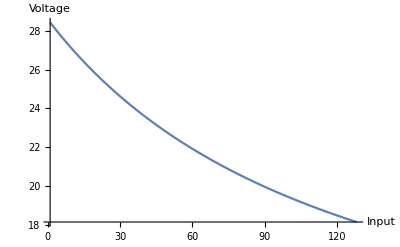

```mathematica
Plot[Vout[input],{input,1,128},AxesLabel->{"Input", "Voltage"}]
```

```mathematica
For[i=0,i<128,i++,Print[{i,Vout[i]}]]
```

{0,28.5976}

{1,28.4355}

{2,28.2759}

{3,28.1187}

{4,27.9639}

{5,27.8113}

{6,27.6611}

{7,27.513}

{8,27.3671}

{9,27.2233}

{10,27.0816}

{11,26.9419}

{12,26.8042}

{13,26.6684}

{14,26.5346}

{15,26.4026}

{16,26.2724}

{17,26.144}

{18,26.0173}

{19,25.8924}

{20,25.7691}

{21,25.6475}

{22,25.5276}

{23,25.4092}

{24,25.2923}

{25,25.177}

{26,25.0631}

{27,24.9508}

{28,24.8398}

{29,24.7303}

{30,24.6222}

{31,24.5154}

{32,24.41}

{33,24.3058}

{34,24.203}

{35,24.1014}

{36,24.001}

{37,23.9019}

{38,23.804}

{39,23.7072}

{40,23.6116}

{41,23.5171}

{42,23.4237}

{43,23.3315}

{44,23.2403}

{45,23.1501}

{46,23.061}

{47,22.9729}

{48,22.8859}

{49,22.7998}

{50,22.7147}

{51,22.6305}

{52,22.5473}

{53,22.465}

{54,22.3836}

{55,22.3031}

{56,22.2234}

{57,22.1447}

{58,22.0668}

{59,21.9897}

{60,21.9135}

{61,21.838}

{62,21.7634}

{63,21.6896}

{64,21.6165}

{65,21.5442}

{66,21.4726}

{67,21.4018}

{68,21.3317}

{69,21.2624}

{70,21.1937}

{71,21.1257}

{72,21.0585}

{73,20.9919}

{74,20.9259}

{75,20.8606}

{76,20.796}

{77,20.732}

{78,20.6686}

{79,20.6059}

{80,20.5437}

{81,20.4822}

{82,20.4212}

{83,20.3609}

{84,20.3011}

{85,20.2419}

{86,20.1832}

{87,20.1251}

{88,20.0675}

{89,20.0105}

{90,19.954}

{91,19.8981}

{92,19.8426}

{93,19.7877}

{94,19.7332}

{95,19.6793}

{96,19.6258}

{97,19.5728}

{98,19.5203}

{99,19.4683}

{100,19.4167}

{101,19.3656}

{102,19.315}

{103,19.2648}

{104,19.215}

{105,19.1657}

{106,19.1168}

{107,19.0683}

{108,19.0202}

{109,18.9726}

{110,18.9253}

{111,18.8785}

{112,18.8321}

{113,18.786}

{114,18.7403}

{115,18.6951}

{116,18.6502}

{117,18.6057}

{118,18.5615}

{119,18.5177}

{120,18.4743}

{121,18.4312}

{122,18.3885}

{123,18.3461}

{124,18.3041}

{125,18.2624}

{126,18.2211}

{127,18.18}